```mathematica
FindInstance[x^y+y^x==p^3,{x,y,p},Integers]
```

FindInstance::nsmet: FindInstance 可使用的方法不足以找到要求的实例或者证明它们不存在.

FindInstance[x^y+y^x==p^3,{x,y,p},ℤ]

```mathematica
Product[Cos[1/i],{i,1,Infinity}]//N
```

0.388536

4497/512

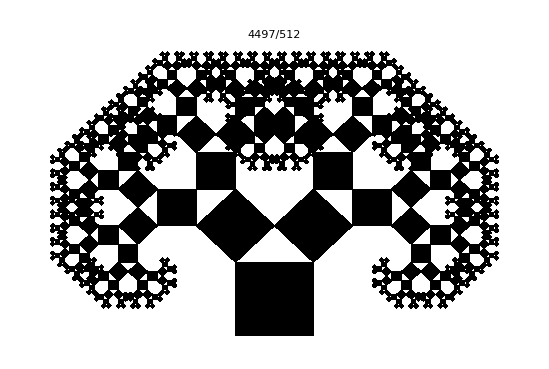

```mathematica
gra=Polygon/@PythagorasTree[n=9];
area=Rationalize[Area[BooleanRegion[Or,DiscretizeRegion[#,AccuracyGoal->10]&/@gra],WorkingPrecision->30]]
Graphics[gra,PlotLabel->Style[area,Red]]
```

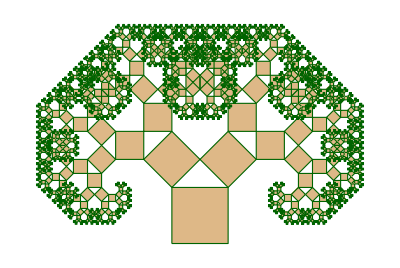

```mathematica
PythagorasTree[depth_,arg_:45°]:=Block[
{pts={{0,0},{1,0},{1,1},{0,1}},t1,t2},
t1=TranslationTransform[{0,1}].ScalingTransform[{Cos@arg,Cos@arg}].RotationTransform[arg];
t2=TranslationTransform[{Cos[arg]^2,Cos[arg]Sin[arg]+1}].ScalingTransform[{Sin@arg,Sin@arg}].RotationTransform[arg-90Degree];
Partition[#,4]&/@NestList[Join[t1@#,t2@#]&,pts,depth]
]


PTG:=Block[{tree=PythagorasTree[#]},
Graphics[{
EdgeForm[ColorData["Legacy","DarkGreen"]],
{FaceForm[ColorData["Legacy","Burlywood"]],
Polygon[Join@@Most@tree]},
{FaceForm[ColorData["Legacy","DarkGreen"]],
Polygon@Last@tree}
}]
]&;
PTG[10]
```

```mathematica
Table[gra=Polygon/@PythagorasTree[n];
area=Area[BooleanRegion[Or,DiscretizeRegion/@gra]],{n,1,10}]
```

{2.,3.,4.,5.,5.9375,6.82813,7.63281,8.22656,8.7832,9.24365}

```mathematica
Manipulate[Plot[Sin[x(1+a x)],{x,0,6}],{n,0,10,1}]
```

```mathematica
1/Product[1-x^k y,{k,1,Infinity}]
```

(1-y)/QPochhammer[y,x]

```mathematica
SeriesCoefficient[(1-y)/QPochhammer[y,x],{x,0,10},{y,0,5}]
```

7

```mathematica
IntegerPartitions[10,{5}]
```

{{6,1,1,1,1},{5,2,1,1,1},{4,3,1,1,1},{4,2,2,1,1},{3,3,2,1,1},{3,2,2,2,1},{2,2,2,2,2}}

```mathematica
IntegerPartitions[10,5]
```

{{10},{9,1},{8,2},{8,1,1},{7,3},{7,2,1},{7,1,1,1},{6,4},{6,3,1},{6,2,2},{6,2,1,1},{6,1,1,1,1},{5,5},{5,4,1},{5,3,2},{5,3,1,1},{5,2,2,1},{5,2,1,1,1},{4,4,2},{4,4,1,1},{4,3,3},{4,3,2,1},{4,3,1,1,1},{4,2,2,2},{4,2,2,1,1},{3,3,3,1},{3,3,2,2},{3,3,2,1,1},{3,2,2,2,1},{2,2,2,2,2}}

```mathematica
Select[IntegerPartitions[10], Max[Length/@Split@ #]==1&]
PartitionsQ[10]
```

{{10},{9,1},{8,2},{7,3},{7,2,1},{6,4},{6,3,1},{5,4,1},{5,3,2},{4,3,2,1}}

10

```mathematica
hadamard
```

```mathematica
GeneratingFunction
```

```mathematica
Table[1/(n!)^2,{n,0,10}]
GeneratingFunction[1/(n!)^2,n,x]
```

{1,1,1/4,1/36,1/576,1/14400,1/518400,1/25401600,1/1625702400,1/131681894400,1/13168189440000}

BesselI[0,2 √x]

```mathematica
SeriesCoefficient[(BesselI[0,2 √x])x,{x,0,n}]
```

Piecewise[{{1/Gamma[n]^2, n≥1}, {0, True}}]

```mathematica
Integrate[F[Sqrt@z Exp[I t]]F[Sqrt@z Exp[-I t]],{t,0,2Pi}]/(2Pi)
```

(∫_0^(2 π) F[ⅇ^(ⅈ t) √z] G[ⅇ^(-ⅈ t) √z]ⅆt)/(2 π)

(∫_0^(2 π) F[ⅇ^(-ⅈ t) √z] F[ⅇ^(ⅈ t) √z]ⅆt)/(2 π)

```mathematica
GeneratingFunction[1/(n!^3),n,x]
GeneratingFunction[n!^3,n,x]
```

ⅇ^x

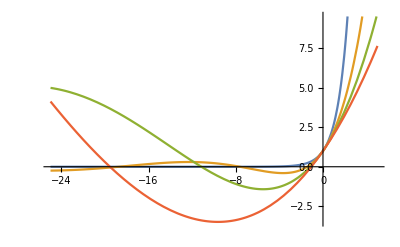

```mathematica
Plot[{
HypergeometricPFQ[{},{},x],
HypergeometricPFQ[{},{1},x],
HypergeometricPFQ[{},{1,1},x],
HypergeometricPFQ[{},{1,1,1},x]
},{x,-25,5}]
```

```mathematica
HypergeometricPFQ[{},{1,1},x]
MeijerG[{{},{}},{{0},{0,0}},-x]
```

HypergeometricPFQ[{},{1,1},x]

HypergeometricPFQ[{},{1,1},x]

```mathematica
MeijerGReduce[HypergeometricPFQ[{},{1,1,1},x],x]
```

HypergeometricPFQ[{},{1,1,1},x]

```mathematica
F[x_]:=E^x;G[x_]:=E^x;
Integrate[F[Sqrt@z Exp[I t]]G[Sqrt@z Exp[-I t]],{t,0,2Pi}]/(2Pi)
%//FullSimplify
%//FunctionExpand
```

(∫_0^(2 π) ⅇ^(ⅇ^(-ⅈ t) √z+ⅇ^(ⅈ t) √z)ⅆt)/(2 π)

Hypergeometric0F1Regularized[1,z]

BesselI[0,2 √z]

```mathematica
Sqrt[210]
```

√210

```mathematica
Integrate[ProductLog'[u]Cos[u],{u,0,Infinity}]
```

∫_0^∞ (Cos[u] ProductLog[u])/(u (1+ProductLog[u]))ⅆu

```mathematica
ProductLog[u]Cos[u]+Integrate[ProductLog[u]Sin[u],{u,0,Infinity}]
```

```mathematica
D[Cos[u],u]
```

-Sin[u]

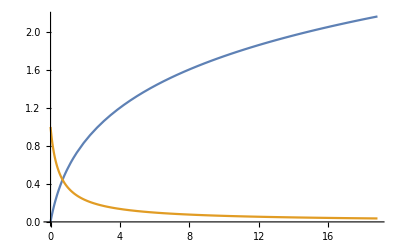

```mathematica
Plot[{ProductLog[u],ProductLog'[u]},{u,0,6Pi}]
```

```mathematica
ArcSin
```

```mathematica
Sqrt@ModularLambda[x I]
```

√ModularLambda[ⅈ x]

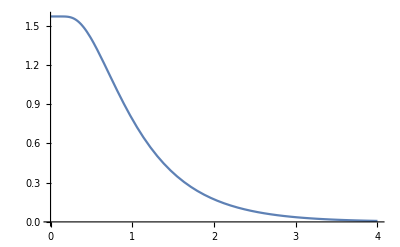

```mathematica
Plot[ArcSin@√ModularLambda[ⅈ x],{x,0,4}]
```

```mathematica
"http://physicise.com/media/anime-girl/bg-42.jpg"
```

http://physicise.com/media/anime-girl/bg-42.jpg

```mathematica
Import["http://physicise.com/media/anime-girl/bg-49.jpg"]
```

-Graphics-

```mathematica
SystemOpen["http://physicise.com/media/anime-girl/bg-42.jpg"]
```

```mathematica
Factorial2
```

```mathematica
0!!
```

1

```mathematica
ToString/@Riffle[{RandomInteger[{0,23}],RandomInteger[{0,59}],RandomInteger[{0,59}]},":"]//StringJoin
SystemOpen["http://localhost:2333"]
```